# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_]:=E^(x+3)/(100 x + 2)
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
Solve[100 x +2==0]
```

{{x→-1/50}}

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x],x->.08∞]
Limit[f[x], x->-∞]
Limit[f[x],x->-1/50, Direction->"FromBelow"]
Limit[f[x],x->-1/50, Direction->"FromAbove"]
```

ⅇ^(3+ .08∞)/(2+100  .08∞)

0

-∞

∞

d. Izračunajte odvod funkcije .

```mathematica
Odvod=D[f[x], x]
D[f[x], x]//N
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

-(100. 2.71828^(3.+x))/(2.+100. x)^2+2.71828^(3.+x)/(2.+100. x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
Solve[Odvod==0,x]
Solve[Odvod==0,x]//N
```

{{x→49/50}}

{{x→0.98}}

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
IntervalNarascanja = Reduce[Odvod>0,x]
IntervalPadanja=Reduce[Odvod<0,x]
(*Ker pada pred in narašča po, vemo, da je 49/50 minimum*)
```

x>49/50

x<-1/50||-1/50<x<49/50

g. Narišite graf funkcije  na intervalu [-5, 5].

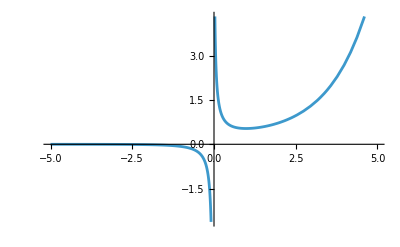

```mathematica
Plot[f[x], {x, -5, 5}]
```

h. Določite zalogo vrednosti funkcije .

```mathematica
Interval[{-∞,Limit[f[x],x->-∞]},{f[49/50],∞}] (*f[49/50 je vključen]*)
```

Interval[{-∞,0},{ⅇ^(199/50)/100,∞}]

i. Izračunajte nedoločeni integral funkcije .

```mathematica
Integrate[f[x], x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll["`*"]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
g[x_]:=(1+x^2.1)/(3+x)
Seznam=Table[g[i],{i,100}]
Round[Mod[21.7,10]]
```

{0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883}

2

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
NovSeznam={}
ClearAll[i]
For[i=1,i<=100,i++,
If[PrimeQ[Floor[Mod[Seznam[[i]],10]]], 
AppendTo[NovSeznam, Seznam[[i]]],
None
]
]
NovSeznam
```

{}

{2.76845,3.79568,7.25393,12.3747,13.7134,15.0702,17.8313,22.0727,23.5093,27.8776,32.3228,33.8198,35.3238,42.9396,47.5778,52.2618,53.8326,55.4079,63.3483,73.005,77.8807,82.7856,87.7183,92.6772,95.9972,97.6613,102.669,107.7,112.754,117.828,122.923,133.171,143.492,145.219,152.146,153.883}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
anon:=#^2+1&
NovSeznam=Map[anon, NovSeznam]
```

{8.66433,15.4072,53.6195,154.134,189.057,228.11,318.954,488.203,553.686,778.158,1045.77,1144.78,1248.77,1844.81,2264.65,2732.29,2898.95,3071.03,4014.01,5330.73,6066.4,6854.46,7695.49,8590.07,9216.47,9538.73,10542.,11600.4,12714.4,13884.4,15111.,17735.4,20591.,21089.6,23149.5,23680.9}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
deljivost=Mod[#,3]==0&
deljivi3=Select[Map[Floor,NovSeznam],Mod[#,3]==0&]
Select[Map[Floor,NovSeznam],deljivost]
Sum[deljivi3[[i]],{i,1,Length[deljivi3]}]
```

Mod[#1,3]==0&

{15,189,228,318,1248,2898,4014,6066,7695,9216,10542,12714,13884}

{15,189,228,318,1248,2898,4014,6066,7695,9216,10542,12714,13884}

69027

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

1+2 x+x^2

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

```mathematica
prepis=x->y+1
```

x→1+y

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

```mathematica
izraz /.x->2
```

9

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

```mathematica
f[x_]:=x^5-4 x^3+x^2+3 x-2
prep={x^n_->2n x^(n-1)}
f[x]/.prep
```

{x^n_→2 n x^(-1+n)}

-2+7 x-24 x^2+10 x^4

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
ClearAll[g, prep]
prep={x^n_->2n x^(n-1)};
g[x_]=x^2025;
g[x]=g[x]//.prep
```

25199184140713966109324439717615969231870192509490767849406134007669090502116720223690823433147324568647885368040234868472725805842375408382714777235818667370000750799297267165516298874435057056626391536083341407086034354955958682263835431941760258054719800578096972937396209464145334192241572534839256708511969052598930072305886602639853383101402921632069724373099652607563860160850638354922808087238654971425101774219020044811168483076705915245408528781053465765686959220085213595325825645754776086514408326545440195205062306924364036505664434061570848962327935913165722289654305888640209925133534626336635435505713127178633684044226041232941592119789855938477549383444472006212451101236135558501147068831093644865400379555901186021070326806533626279865761344623690356572746289168907516209675279484432401064230903437279808760641525685377825853870241756111471353448110147208868096793711163561246968674526934987540452806670537204928185295614192270273731457467374837359983703583401230885852625994172019545836838149058121805888171240017631456801775603021035657543659149163444642609687539227991190696727267788860964719327156982910859191950789849367397175125444831567800030133816248636423457266624421250450356817053841035971385518529511156063665481958342875766993473522734552131920882042790159489709367782626922853899994331466640086999257107852592255380908824028510340588409110195055344828312904113756071338420629068087780705473770891073051175947673764970164992457067216870404174595840737543458631743701439027616098635496855772885923778055855640998741624210083027605176696467062974342730283411372393019788121193931454258408612299649856674530132445979675277111530784584334555295902970365075863846099541939700411558791891099490349114132476289338444711572504507068090299291915601571575050265572475627652553496639688278685485555342994927947515099308806020923451047933680263532372896538915039567894982295608271133256339406694582248505444225175520618016319544052987304782315549530655299604854185657125263385350855383313053522930893826944501805788204889586232231621353947152688354554821348023754561140027652225557987424210217430078191652981018835977203349827791997397831755300842427118789974838452667556816096532477699694780692872081428909713256383684086382750143592718630822790249067628113971178996116661164429572214172021144362975718908758918732259975218610032068250154753671381289499363211212544918554906527649142488437195861743124110611926303643632698779566297831604891887835987792011711493576384051779164997450123928495755237903050176564773974822030345559458096535957217425346233313341864719926607048169573250121789292628743531525583151519953853207714722401963939375068669133067236386986610736363800474691883053455574817451572633328077457900898806425911050751058398907736533933621123555747082103950289922053851873681093991896403039447346523464443246126896873684738902265877309905368794616471261313192710762319162762012002603910076199681899236172438626194520869861899963221180140899239377138506230461881911245689387721475528983229254688544365596157373215610219473857547810833108800706959271748640488835316873641694943156345079373403970191946351280201608949230502646882698621138359976248410148678202760870095074301648275380751631601142449241653771118966448194547719799372734734031692400490534129976626834528845809425808424837609070734028016420510060062340404064432822758704778019389096222115383258516123777079703105970568984075791505716164023094125555618474249401192387487323754246341646559389480510119568107032478290624914121972104123840203726927317442187716594186176883824386859731670044440541024970794898822529547388912407173963601558682959647683671956321180111953756131184684927919134500950141740120023015207537020941616320702727375653965582417529819625736312978424624678898444025172880847484041102336158172901585880116664780154940235873064101225286918853544301958103010030433664324526269070704130937723936914626587611008323471127609260992234843864792650252141938328607454272561003752252856366773469367116134186676608342596589179005703376544813133598691984703814143762072038911008138691525788504937199002598544332739546339635656797495583303877052174036434903685773152746097316644292984960270880117462117199358078094111367293533508290728754178608632942285585330263397125938820295892987340799884603900201639124248078748845879706377746330339504844007218168672957359486135558499573267507805353805338403933393045636366390031361088501766633696152756952896652400268556897520591015662419941672049101786309437962568331143941413129075071968375648007955222657601566892219194143775712028182308005265314167645934013066614260441005838752448458024988242213676852256603205557535026588421324286976947261082959783514609345697265240824438845724170716073184732669005814417955499444896138379313404266063857739357041639184987944699944708217879228883080457826051467540255876343497072706560895764575185971409016110032210219156385648026347674108024600072382311953524546155148967805684860857607949990993168867685353782243877458251208450038181807541141510947441542697337277763057880611598299786062875780936930956206561811740587769326550029896504577429015345647880649529877837814476239548089240279527332717699252071115717138866472777289380550933609576620224718248487199508077504430637812751077562400775521499758225376549279427239888120476683801821824452573492598147838596922302766044903104404659569170135786978104632363575685371266783131742921697473898744826470650941268018722566862283484421476693506221646320637252536012883909963885278758019834783453161773625122316724183935090789804683103396398315627396539714108621338961678338783801504807156643947355924959150610515492030588427583339059655212279447542029241287957999448453335229072120444198588444728444336581297010699405097112586532110020192174295377779849092571877013774177096811122133993887552905538546342074962918078939389669103370450441524830799968561015054436233354196370942710662036190953335685120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 x

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
ClearAll[prep,Fib]
Fib[0]=1
Fib[1]=1
prep:=Fib[n_]->Fib[n-1]+Fib[n-2];
Fib[10]//.prep
```

1

1

89